```mathematica
cs0 = x/.First@FindRoot[LegendreP[1/2,x]==0,{x,-0.5},WorkingPrecision->50]
dd=2.7142175397111330*(-0.5) * LegendreP[1/2,(-cs0)]/(1-(Abs@cs0)^2)^(1/4);
```

-0.65222953196994067235474647720151281206818103290662

```mathematica
Cot@ArcCos@cs0
```

-0.8604366861256782695832923224100689509020553793886

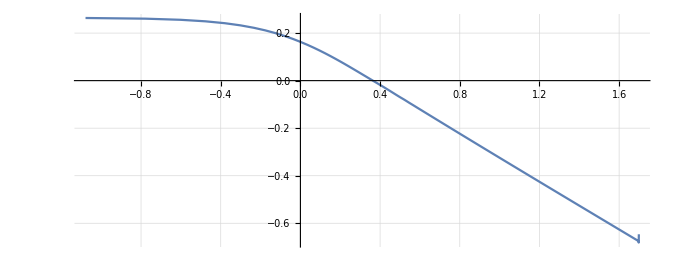

FittedModel[0.140422-0.474923 t]

```mathematica
SetDirectory[NotebookDirectory[]];
res=Import["res.txt","Table"];
ListPlot[Log10@Abs@res⟦1;;-1;;1⟧,PlotRange->All,Joined->True,AspectRatio->Automatic,GridLines->Automatic]
LinearModelFit[Log10@Abs@res⟦2;;-1;;1⟧,t,{t}]
```

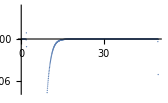

```mathematica
ListPlot@res
```

-0.9208

-0.920795

-0.92468

-0.71691

-0.71691

0

{{0,-2.08454},{0.520687,-1.78046},{1,-1.41626},{1.50538,-1.19676},{2,-1.07609},{2.5062,-0.967939},{3,-0.876551},{3.50115,-0.807239},{4,-0.755266},{4.50111,-0.711373},{5,-0.673865},{5.50053,-0.64164},{6,-0.613882},{6.50039,-0.589346},{7,-0.567547},{7.50026,-0.547969},{8,-0.530323},{8.50019,-0.514257},{9,-0.499585},{9.50015,-0.486088},{10,-0.473641},{10.5001,-0.462097},{11,-0.451364},{11.5001,-0.441342},{12,-0.431964},{12.5001,-0.423157},{13,-0.414871},{13.5001,-0.407051},{14,-0.39966},{14.5001,-0.392656},{15,-0.38601},{15.5,-0.379689},{16,-0.373671},{16.5,-0.367929},{17,-0.362445},{17.5,-0.357198},{18,-0.352174},{18.5,-0.347356},{19,-0.342731},{19.5,-0.338285},{20,-0.334009},{20.5,-0.329891},{21,-0.325922},{21.5,-0.322092},{22,-0.318395},{22.5,-0.314822},{23,-0.311367},{23.5,-0.308024},{24,-0.304786},{24.5,-0.301647},{25,-0.298605},{25.5,-0.295652},{26,-0.292785},{26.5,-0.29},{27,-0.287294},{27.5,-0.284661},{28,-0.2821},{28.5,-0.279607},{29,-0.277179},{29.5,-0.274813},{30,-0.272506},{30.5,-0.270257},{31,-0.268062},{31.5,-0.265921},{32,-0.263829},{32.5,-0.261787},{33,-0.259791},{33.5,-0.25784},{34,-0.255932},{34.5,-0.254066},{35,-0.252241},{35.5,-0.250454},{36,-0.248705},{36.5,-0.246992},{37,-0.245313},{37.5,-0.243669},{38,-0.242057},{38.5,-0.240477},{39,-0.238927},{39.5,-0.237407},{40,-0.235916},{40.5,-0.234452},{41,-0.233016},{41.5,-0.231605},{42,-0.23022},{42.5,-0.228859},{43,-0.227522},{43.5,-0.226209},{44,-0.224917},{44.5,-0.223648},{45,-0.2224},{45.5,-0.221173},{46,-0.219966},{46.5,-0.218778},{47,-0.217609},{47.5,-0.216459},{48,-0.215327},{48.5,-0.214213},{49,-0.213116},{49.5,-0.212035},{50,-0.210973}}

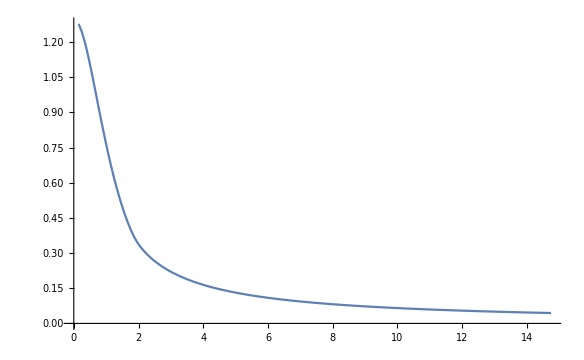

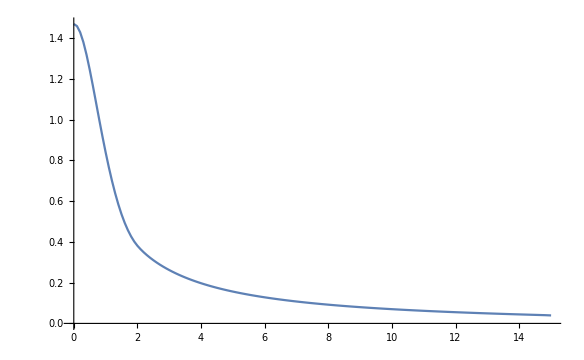

```mathematica
res⟦1,2⟧/2
```

```mathematica
(1/250/(1/200))^2//N
```

0.64

```mathematica
res
```

{{0,-0.259207},{0.2,-0.267034},{0.4,-0.290761},{0.6,-0.331147},{0.8,-0.389573},{1,-0.468233},{1.2,-0.570451},{1.4,-0.701104},{1.6,-0.869197},{1.8,-1.09312},{2,-1.35772},{2.2,-1.57306},{2.4,-1.74627},{2.6,-1.9221},{2.8,-2.1092},{3,-2.29354},{3.2,-2.474},{3.4,-2.65441},{3.6,-2.83428},{3.8,-3.01339},{4,-3.19196},{4.2,-3.37007},{4.4,-3.54776},{4.6,-3.72507},{4.8,-3.90206},{5,-4.07874},{5.2,-4.25516},{5.4,-4.43134},{5.6,-4.60729},{5.8,-4.78304},{6,-4.95861},{6.2,-5.13401},{6.4,-5.30925},{6.6,-5.48435},{6.8,-5.65931},{7,-5.83415},{7.2,-6.00888},{7.4,-6.1835},{7.6,-6.35801},{7.8,-6.53244},{8,-6.70677},{8.2,-6.88103},{8.4,-7.0552},{8.6,-7.2293},{8.8,-7.40334},{9,-7.5773},{9.2,-7.75121},{9.4,-7.92506},{9.6,-8.09885},{9.8,-8.27259},{10,-8.44628},{10.2,-8.61993},{10.4,-8.79352},{10.6,-8.96708},{10.8,-9.1406},{11,-9.31407},{11.2,-9.48751},{11.4,-9.66091},{11.6,-9.83428},{11.8,-10.0076},{12,-10.1809},{12.2,-10.3542},{12.4,-10.5274},{12.6,-10.7007},{12.8,-10.8739},{13,-11.047},{13.2,-11.2202},{13.4,-11.3933},{13.6,-11.5664},{13.8,-11.7394},{14,-11.9125},{14.2,-12.0855},{14.4,-12.2585},{14.6,-12.4315},{14.8,-12.6045},{15,-12.7775},{15.2,-12.9504},{15.4,-13.1233},{15.6,-13.2962},{15.8,-13.4691},{16,-13.642},{16.2,-13.8149},{16.4,-13.9877},{16.6,-14.1605},{16.8,-14.3334},{17,-14.5062},{17.2,-14.679},{17.4,-14.8517},{17.6,-15.0245},{17.8,-15.1973},{18,-15.37},{18.2,-15.5428},{18.4,-15.7155},{18.6,-15.8882},{18.8,-16.0609},{19,-16.2336},{19.2,-16.4063},{19.4,-16.579},{19.6,-16.7516},{19.8,-16.9243},{20,-17.0969},{20.2,-17.2696},{20.4,-17.4422},{20.6,-17.6148},{20.8,-17.7875},{21,-17.9601},{21.2,-18.1327},{21.4,-18.3053},{21.6,-18.4779},{21.8,-18.6504},{22,-18.823},{22.2,-18.9956},{22.4,-19.1681},{22.6,-19.3407},{22.8,-19.5132},{23,-19.6858},{23.2,-19.8583},{23.4,-20.0309},{23.6,-20.2034},{23.8,-20.3759},{24,-20.5484},{24.2,-20.7209},{24.4,-20.8934},{24.6,-21.0659},{24.8,-21.2384},{25,-21.4109},{25.2,-21.5834},{25.4,-21.7559},{25.6,-21.9284},{25.8,-22.1008},{26,-22.2733},{26.2,-22.4458},{26.4,-22.6182},{26.6,-22.7907},{26.8,-22.9631},{27,-23.1356},{27.2,-23.308},{27.4,-23.4804},{27.6,-23.6529},{27.8,-23.8253},{28,-23.9977},{28.2,-24.1702},{28.4,-24.3426},{28.6,-24.515},{28.8,-24.6874},{29,-24.8598},{29.2,-25.0322},{29.4,-25.2046},{29.6,-25.377},{29.8,-25.5494}}

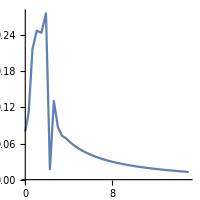

```mathematica
ListPlot[res⟦1;;-1;;2⟧,Joined->True,PlotRange->All,AspectRatio->1]
```

81

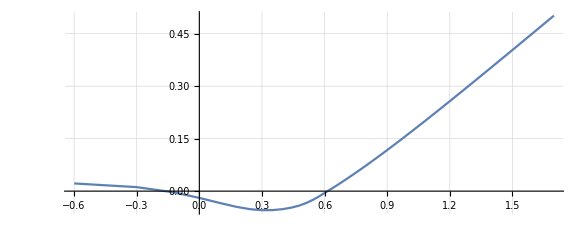

```mathematica
Length@res
```

```mathematica
ArcCos@cs0
```

2.2813183068406470463924167927275591485937279252011

```mathematica
ff=c0 r+c1 /√r;
Series[D[ff,{r,2}]/((√(1+D[ff,{r,1}]^2))^3)+1/r D[ff,r]/(√(1+D[ff,{r,1}]^2)),{r,∞,5}]
```

c0/(√(1+c0^2) r)+(c1 (1/r)^(5/2))/(4 (1+c0^2)^(3/2))+(3 c0 c1^2)/(4 (1+c0^2)^(5/2) r^4)+O[1/r]^(11/2)

```mathematica
100*4+99+92.5
```

591.5

```mathematica
-0.275783438603136*c1+0.210659453420660*b0*b0*c1-0.069483517708871*c1*c1*c1/.c1->-0.5
```

0.146577-0.10533 b0^2

```mathematica
(63+88+77+82.5+0+98+0+95)/6
```

83.9167

```mathematica
Solve[2.714217539711130*c1 == -2.37,c1]
```

{{c1→-0.87318}}